```mathematica
point1={-1,1}
point2={1,2}
```

{-1,1}

{1,2}

```mathematica
a=(point2[[2]]-point1[[2]])/(point2[[1]]-point1[[1]])
```

1/2

```mathematica
b=point1[[2]]-a*point1[[1]]
```

3/2

```mathematica
circumference[x_][y_] = (x-1/2)^2+(y-1/2)^2
f[x_] = a*x+b
```

(-1/2+x)^2+(-1/2+y)^2

3/2+x/2

```mathematica
equation=Solve[{y==f[x],circumference[x][y]== 2^2},{x,y}] //N
```

{{x→-1.48324,y→0.75838},{x→1.48324,y→2.24162}}

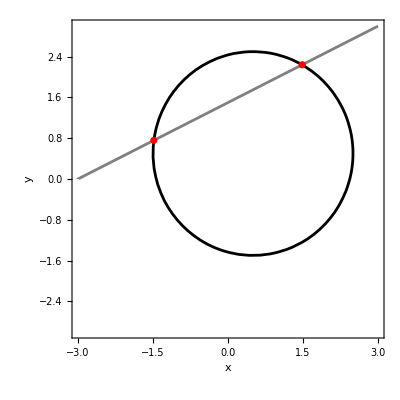

```mathematica
Show[ContourPlot[{y==f[x],circumference[x][y]==2^2},{x,-3,3},{y,-3,3},ContourStyle->{Gray,Black},PlotRange->{{-3,3},{-3,3}},Axes->True,AxesLabel->{"x","y"},AspectRatio->1],ListPlot[{x,y}/. equation,PlotStyle->Red]]
```